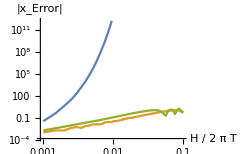
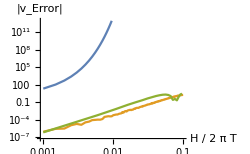
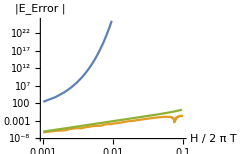
-Graphics- | -Graphics-
-Graphics- |

```mathematica
SetDirectory[NotebookDirectory[]];
d=Import/@FileNames["A_*.dat"];

Grid[{{
ListLinePlot[
Abs@d[[All,All,{1,2}]],
PlotRange->All,
ScalingFunctions->{"Log","Log"},
AxesLabel->{"H / 2 π T","|x_Error|"},
ImageSize->250
],
ListLinePlot[
Abs@d[[All,All,{1,3}]],
PlotRange->All,
ScalingFunctions->{"Log","Log"},
AxesLabel->{"H / 2 π T","|v_Error|"},
ImageSize->250
]
},{
ListLinePlot[
Abs@d[[All,All,{1,4}]],
PlotRange->All,
ScalingFunctions->{"Log","Log"},
AxesLabel->{"H / 2 π T","|E_Error |"},
ImageSize->250
],
LineLegend[ColorData[97,"ColorList"],{"explizites Euler Verfahren","Leap Frog Verfahren", "Runge Kutta Verfahren\n(2.Ordnung)","Verlet Verfahren" }]
}}]
Export["A_plot.png",%];
```

```mathematica
SetDirectory[NotebookDirectory[]];
d=Import@FileNames["C_*.dat"][[1]];
d=DeleteCases[d, {}];
ByteCount@d

Row[{
ListDensityPlot[d[[All,{1,2,3}]],PlotLegends->BarLegend[Automatic,LegendMarkerSize->180],ColorFunction->"SunsetColors",PlotLabel->"Amplitude",FrameLabel->{"γ","ω_t/ω_E"},PlotRange->{{0.05,5},All,{0,5}},ScalingFunctions->"SignedLog",ImageSize->200,
MeshFunctions->{#3&},Mesh->15,MeshStyle->White
],
ListDensityPlot[#-{0,0,Pi}&/@d[[All,{1,2,4}]],PlotLegends->BarLegend[Automatic,LegendMarkerSize->180],ColorFunction->Hue,PlotLabel->"Phasenverschiebung",FrameLabel->{"γ","ω_t/ω_E"},ImageSize->200,PlotRange->{{0.05,5},All,{-Pi,Pi}},
MeshFunctions->{#3&},Mesh->0,MeshStyle->White
]
 }
]
Export["C_Plot.png",%,RasterSize->1000];
```

5299280

-Graphics--Graphics-

```mathematica
ListPlot3D[d[[All,{1,2,3}]],ColorFunction->"SunsetColors",AxesLabel->{"γ","ω_t/ω_E","A/A_t"},PlotRange->{{0.05,5},{0.05,All},{0,5}},Boxed->False,MeshFunctions->{#3&},MeshStyle->White,Mesh->15,MaxPlotPoints->200,PlotLegends->BarLegend[Automatic,LegendMarkerSize->180]
]
Export["C_3D.png",%,RasterSize->1000];
```

-Graphics3D-

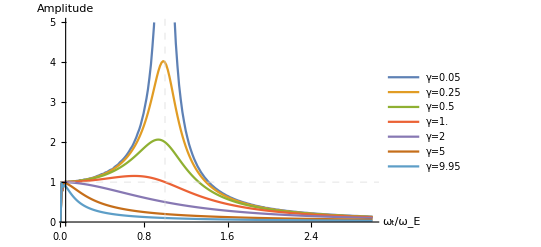

```mathematica
ListLinePlot[
Evaluate@Table[Select[d[[All,{1,2,3}]],#[[1]]==i&][[All,{2,3}]],{i,{0.05,0.25,0.5,1.0,2,5,9.95}}],PlotRange->{{0.05,All},{0,5}},AxesLabel->{"ω_t/ω_E","Amplitude"},
PlotLegends->(("γ="<>ToString@#)&/@{0.05,0.25,0.5,1.0,2,5,9.95}),
GridLines->{{1},{1}},GridLinesStyle->Dashed
]
Export["C_Seite.png",%,RasterSize->1000];
```